```mathematica
Print[Button[Style["Quit Kernel",Bold],Quit[],ImageSize->{150,35}]]
```

Quit Kernel

Regressive Näherung von Daten (Messdatenreihe oder diskretisierte Funktion) durch möglichst einfache nicht periodische Funktion ϕ(x). Im folgenden Programm wird eine nach dem n_-/n_+-ten Glied abgebrochene Laurent-Reihe verwendet:

ϕ[x]=∑_(i=-n_-)^(n_+) c_i·x^i

Für n_-<0 darf in den Daten kein Punkt an der Stelle x=0 vorhanden sein.
Für n_-=0 vereinfacht sich diese zu einer nach dem n-ten Glied abgebrochene Mac-Laurin-Reihe bzw. Taylor-Reihe:

ϕ[x]=∑_(i=0)^n c_i·x^i

Für n=0 ergibt sich der Mittelwert der Daten.
Es resultiert ein überbestimmtes Gleichungssystem, woraus sich folgende Bedingung ableiten lässt:

Anzahl  der Datenpunkte > Anzahl der Summanden von ϕ(x)

## Eingabe (𝒹𝒶𝓉ℯ𝓃)

```mathematica
ClearAll["Global`*"]
𝒹𝒶𝓉ℯ𝓃=Table[{x,1+3x+5/x^2+RandomReal[.5]},{x,0.4,7,0.2}];
```

## Plot

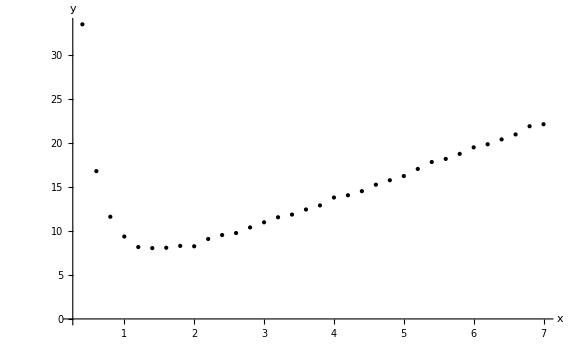

```mathematica
(*Ausgabe*)
plotDaten=ListPlot[𝒹𝒶𝓉ℯ𝓃,
PlotStyle->{Black,PointSize->Medium},AxesLabel->{"x","y"},PlotRange->All,ImageSize->Large];
Print[Show[plotDaten]]
```

## Programm (automatisch)

```mathematica
𝓃={-2,3};
```

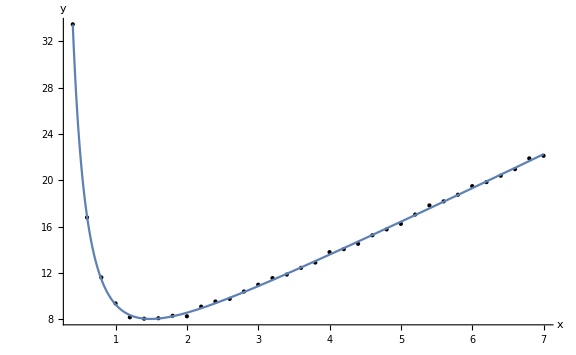

ϕ(x) = 1.10036+4.92027/x^2+0.14609/x+3.14745 x-0.0384618 x^2+0.00260385 x^3
ρ = 0.135332

```mathematica
(*Programm*)
𝒻𝓊𝓃𝓀𝓉𝒾ℴ𝓃ℯ𝓃=Table[x^i,{i,𝓃[[1]],𝓃[[2]]}];
ϕ[x_]=Fit[𝒹𝒶𝓉ℯ𝓃,𝒻𝓊𝓃𝓀𝓉𝒾ℴ𝓃ℯ𝓃,x];
ρ=√(1/Length[𝒹𝒶𝓉ℯ𝓃] Sum[(𝒹𝒶𝓉ℯ𝓃[[i,2]]-ϕ[𝒹𝒶𝓉ℯ𝓃[[i,1]]])^2,{i,Length[𝒹𝒶𝓉ℯ𝓃]}]);

(*Ausgabe*)
plot=Plot[ϕ[x],
{x,Min[𝒹𝒶𝓉ℯ𝓃[[All,1]]],Max[𝒹𝒶𝓉ℯ𝓃[[All,1]]]},
PlotRange->All];
Print[Show[plotDaten,plot,PlotRange->All]]
Print[StringForm["ϕ(x) = ``\nρ = ``",ϕ[x],ρ]]
```

## Programm (manuell)

```mathematica
𝓃={-2,3};
```

```mathematica
(*Programm*)
𝒜=Table[If[j==0,1,𝒹𝒶𝓉ℯ𝓃[[i,1]]]^j,{i,Length[𝒹𝒶𝓉ℯ𝓃]},{j,𝓃[[1]],𝓃[[2]]}];
𝒷=𝒹𝒶𝓉ℯ𝓃[[All,2]];
𝒸=LeastSquares[𝒜,𝒷];
ϕ[x_]=Sum[𝒸[[i+1+Abs[𝓃[[1]]]]] x^i,{i,𝓃[[1]],𝓃[[2]]}];
ρ=√(1/Length[𝒹𝒶𝓉ℯ𝓃] Sum[(𝒹𝒶𝓉ℯ𝓃[[i,2]]-ϕ[𝒹𝒶𝓉ℯ𝓃[[i,1]]])^2,{i,Length[𝒹𝒶𝓉ℯ𝓃]}]);

(*Ausgabe*)
plot=Plot[ϕ[x],
{x,Min[𝒹𝒶𝓉ℯ𝓃[[All,1]]],
Max[𝒹𝒶𝓉ℯ𝓃[[All,1]]]},PlotRange->All];
Print[Show[plotDaten,plot,PlotRange->All]]
Print[StringForm["ϕ(x) = ``\nρ = ``",ϕ[x],ρ]]
```

-Graphics-

ϕ(x) = 1.10036+4.92027/x^2+0.14609/x+3.14745 x-0.0384618 x^2+0.00260385 x^3
ρ = 0.135332

## Programm (Vergleich)

```mathematica
𝓃={-2,6};
```

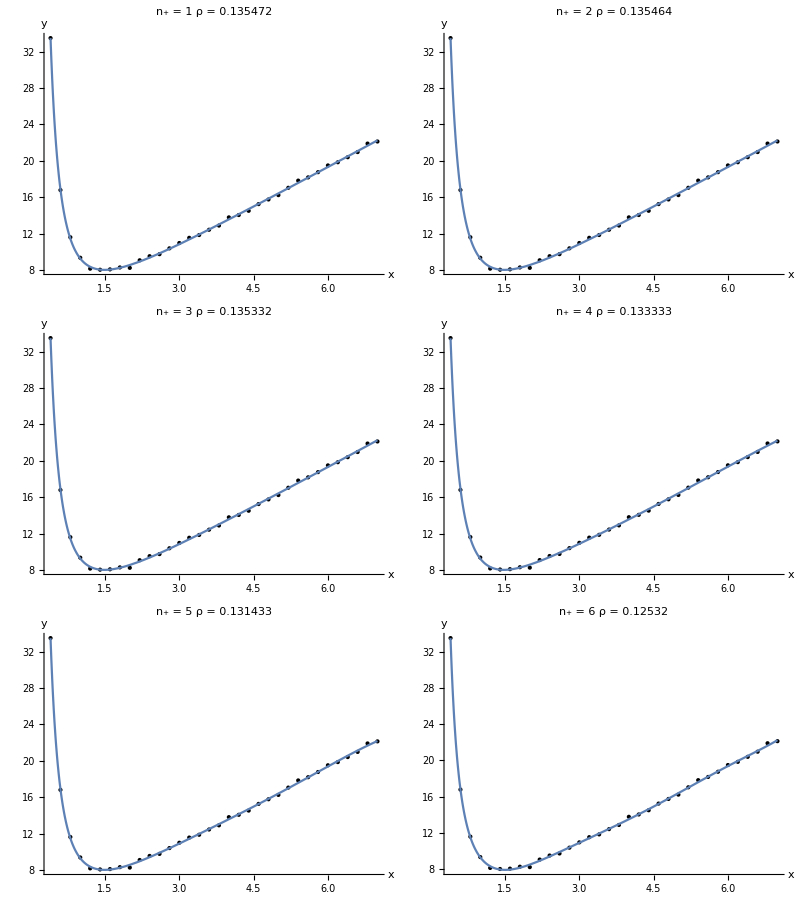

```mathematica
Print[TableForm[Partition[Table[
(*Programm*)
𝒻𝓊𝓃𝓀𝓉𝒾ℴ𝓃ℯ𝓃=Table[x^i,{i,𝓃[[1]],j}];
ϕ[x_]=Fit[𝒹𝒶𝓉ℯ𝓃,𝒻𝓊𝓃𝓀𝓉𝒾ℴ𝓃ℯ𝓃,x];
ρ=√(1/Length[𝒹𝒶𝓉ℯ𝓃] Sum[(𝒹𝒶𝓉ℯ𝓃[[i,2]]-ϕ[𝒹𝒶𝓉ℯ𝓃[[i,1]]])^2,{i,Length[𝒹𝒶𝓉ℯ𝓃]}]);

(*Ausgabe*)
plot=Plot[ϕ[x],
{x,Min[𝒹𝒶𝓉ℯ𝓃[[All,1]]],Max[𝒹𝒶𝓉ℯ𝓃[[All,1]]]},
PlotRange->All];
Show[plotDaten,plot,PlotRange->All,PlotLabel->StringForm["n_+ = ``\nρ = ``",j,ρ],ImageSize->Medium]
,{j,If[Mod[𝓃[[2]],2]==0,𝓃[[2]],𝓃[[2]]+1]}],2]]]
```